# Optimal parameter lookup and Limit

## Version 2.0.0

JSON Import

```mathematica
OpenJSONDialog[]:=SystemDialogInput["FileOpen",{"simdata.json",{"RiverSim files"->{"*.json"}}}]
```

```mathematica
OpenJSONDialog[]
```

/home/oleg/dev/build/simdata.json

```mathematica
data = Import[SystemDialogInput["FileOpen"],"RawJSON"];
```

```mathematica
data = Import[SystemDialogInput["FileOpen"],"RawJSON"];
```

```mathematica
Keys[data]
```

{Border,Description,GeometryDifference,Model,RuntimeInfo,Trees,Version}

Visualize and process input JSON

### Plots simulation data structure. Single or list of simulations data

```mathematica
plotSimData[data_]:=
ListPlot[
data["Trees"]["Branches"][[All,"coords"]],
Joined->True,
PlotRange->{{0,data["Model", "width"]},{0,data["Model", "height"]}}, 
AspectRatio->1, 
Joined->True];
```

```mathematica
plotJSON[filePath_]:=
plotSimData[Import[filePath, "RawJSON"]];
```

### TODO

JSON Export

```mathematica
Options[ModelJSONStructure] = {
"dx"->0.2,
"width"->1,
"height"->1,
"riverBoundaryId"->4,
"boundaryIds"->{1,2,3,4},
"boundaryCondition"->0,
"fieldValue"->1,
"eta"->0,
"biffurcationType"->0,
"biffurcationThreshold"->-0.2,
"biffurcationThreshold2"->0.0001,
"biffurcationMinDistance"->0.07,
"biffurcationAngle"->Pi/5.,
"growthType"->0,
"growthThreshold"->0,
"growthMinDistance"->0.03,
"ds"->0.005,

"integrRadius"->0.03,
"integrExponant"->3,
"weightRadius"->0.02,

"meshEps"->1. 10^-5,
"meshExponant"->3,
"meshRefinmentRadius"->0.2,
"meshMinArea"->1. 10^-9,
"meshMaxArea"->1. 10,
"meshMinAngle"->32,

"quadratureDegree"->3,
"refinmentFraction"->0.1,
"refinmentSteps"->3
};
ModelJSONStructure[OptionsPattern[]]:={
"Model"->{
"width"->OptionValue["width"],
"height"->OptionValue["height"],
"dx"->OptionValue["dx"],
"riverBoundaryId"->OptionValue["riverBoundaryId"],
"boundaryIds"->OptionValue["boundaryIds"],

"boundaryCondition"->OptionValue["boundaryCondition"],
"fieldValue"->OptionValue["fieldValue"],
"eta"->OptionValue["eta"],
"biffurcationType"->OptionValue["biffurcationType"],
"biffurcationThreshold"->OptionValue["biffurcationThreshold"],
"biffurcationThreshold2"->OptionValue["biffurcationThreshold2"],
"biffurcationAngle"->OptionValue["biffurcationAngle"],
"biffurcationMinDistance"->OptionValue["biffurcationMinDistance"],
"growthType"->OptionValue["growthType"],
"growthThreshold"->OptionValue["growthThreshold"],
"growthMinDistance"->OptionValue["growthMinDistance"],
"ds"->OptionValue["ds"],

"Mesh"->{
"eps"->OptionValue["meshEps"],
"refinmentRadius"->OptionValue["meshRefinmentRadius"],
"minArea"->OptionValue["meshMinArea"],
"maxArea"->OptionValue["meshMaxArea"],
"minAngle"->OptionValue["meshMinAngle"],
"exponant"->OptionValue["meshExponant"]
},

"Integration"->{
"radius"->OptionValue["integrRadius"],
"weightRadius"->OptionValue["weightRadius"],
"exponant"->OptionValue["integrExponant"]},

"Solver"->{
"quadratureDegree"->OptionValue["quadratureDegree"],
"refinmentFraction"->OptionValue["refinmentFraction"],
"refinmentSteps"->OptionValue["refinmentSteps"]}
}};
```

### Test and example of usage

```mathematica
ModelJSONStructure["dx"->0.19]
```

{Model→{width→1,height→1,dx→0.19,riverBoundaryId→4,boundaryIds→{1,2,3,4},boundaryCondition→0,fieldValue→1,eta→0,biffurcationType→0,biffurcationThreshold→-0.2,biffurcationThreshold2→0.0001,biffurcationAngle→0.314159,biffurcationMinDistance→biffurcationMinDistance,growthType→0,growthThreshold→0,growthMinDistance→0.03,ds→0.005,Mesh→{eps→0.00001,refinmentRadius→0.2,minArea→1.×10^-8,maxArea→10.,minAngle→32,exponant→3},Integration→{radius→0.03,weightRadius→0.02,exponant→3},Solver→{quadratureDegree→3,refinmentFraction→0.1,refinmentSteps→3}}}

```mathematica
Export[NotebookDirectory[]<>"test.json",ModelJSONStructure[]]
```

/home/oleg/dev/riversim/research/test.json

```mathematica
mdl=Import[NotebookDirectory[]<>"test.json","RawJSON"]
```

<|Model→<|width→1,height→1,dx→0.2,riverBoundaryId→4,boundaryIds→{1,2,3,4},boundaryCondition→0,fieldValue→1,eta→0,biffurcationType→0,biffurcationThreshold→-0.2,biffurcationThreshold2→0.0001,biffurcationAngle→0.314159,biffurcationMinDistance→biffurcationMinDistance,growthType→0,growthThreshold→0,growthMinDistance→0.03,ds→0.005,Mesh→<|eps→0.00001,refinmentRadius→0.2,minArea→1.×10^-8,maxArea→10.,minAngle→32,exponant→3|>,Integration→<|radius→0.03,weightRadius→0.02,exponant→3|>,Solver→<|quadratureDegree→3,refinmentFraction→0.1,refinmentSteps→3|>|>|>

```mathematica
mdl["Model","width"]
```

1

Runner

### This function calls riversim program and communicate with it through file

```mathematica
RunSimulation[numOfSteps_:10, modelParams_:ModelJSONStructure[], outputName_:"simdata"]:=Module[{
resultDir="/home/oleg/dev/build",
riversimPath= "/home/oleg/dev/build/source/riversim",
exportJSONPath = "/home/oleg/dev/build/mathematica_model_params.json",
importJSONPath = "/home/oleg/dev/build/"<>outputName<>".json",
log},
Export[
exportJSONPath,
modelParams
];
log=RunProcess[{
riversimPath, 
"-o",outputName,
"-n",numOfSteps,
exportJSONPath},
ProcessDirectory->resultDir
];
Import[importJSONPath,"RawJSON"]
];
```

```mathematica
data1=RunSimulation[30, ModelJSONStructure["ds"->0.04444], "testdata"];
data2=RunSimulation[100, ModelJSONStructure["ds"->0.01], "testdata"];
```

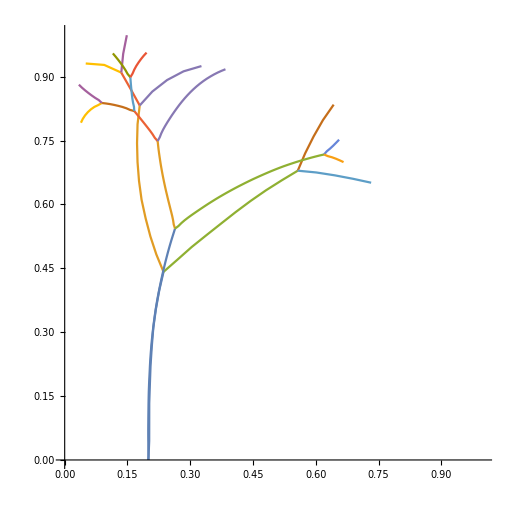

```mathematica
Show[plotSimData[#]&/@{data1, data2}]
```

### This is GUI interface for simulation and its data

```mathematica
Manipulate[
plotSimData@
RunSimulation[n, ModelJSONStructure["ds"->ds, "dx"->0.4], outputname],
{ds, 0.001, 0.1},
{n,3,150,10},
{outputname, "simdata"}
]
```

# Comparing results with analytical solution

```mathematica
cc[z_,a0_]:=-Sqrt[Cos[Pi z/2]]/Sin[Pi*a0/2]-EllipticF[Pi*z/4,2];
solvak[a0_,t_,gamma_]:=ⅇ^((-π^2 t)/8)((cc[gamma,a0]+EllipticF[1/2 ArcSin[ⅇ^(-(π^2 t)/8) Sin[(a0 π)/2]],2]) Sin[(a0 π)/2])/((1-ⅇ^(-(π^2 t)/4) Sin[(a0 π)/2]^2)^(1/4));
krzy[t_]:=FindRoot[solvak[0.5,t,gamma]==-1,{gamma,0.01+0.48*I}][[1,2]];
```

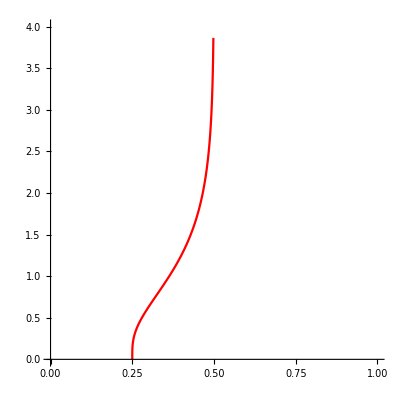

```mathematica
testGrowthPlot = ListPlot[
Table[
{-Re[krzy[t]]*0.5+0.5,0.5*Im[krzy[t]]},
{t,0,4.64999999999,.01}],
Joined->True,
AspectRatio->1,
PlotStyle->{Red},
PlotRange->{{0,1},{0,4}}]//Quiet
```

```mathematica
testsimdata = RunSimulation[600, ModelJSONStructure["dx"->0.25, "biffurcationType"->3, "fieldValue"->0, "boundaryCondition"->1(*Laplacea*), "width"->1, "height"->30]];
```

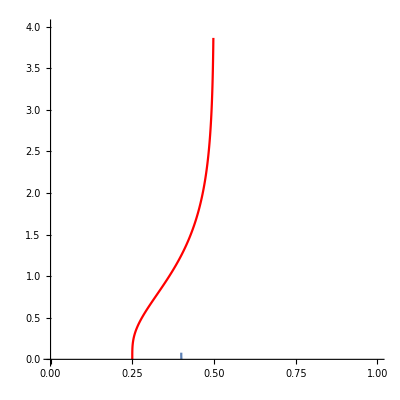

```mathematica
sim=plotJSON[OpenJSONDialog[]];
Show[testGrowthPlot, sim]
```

# Numerical Parameters Limit

### Different values for ds.. from 0.01 to 0.001

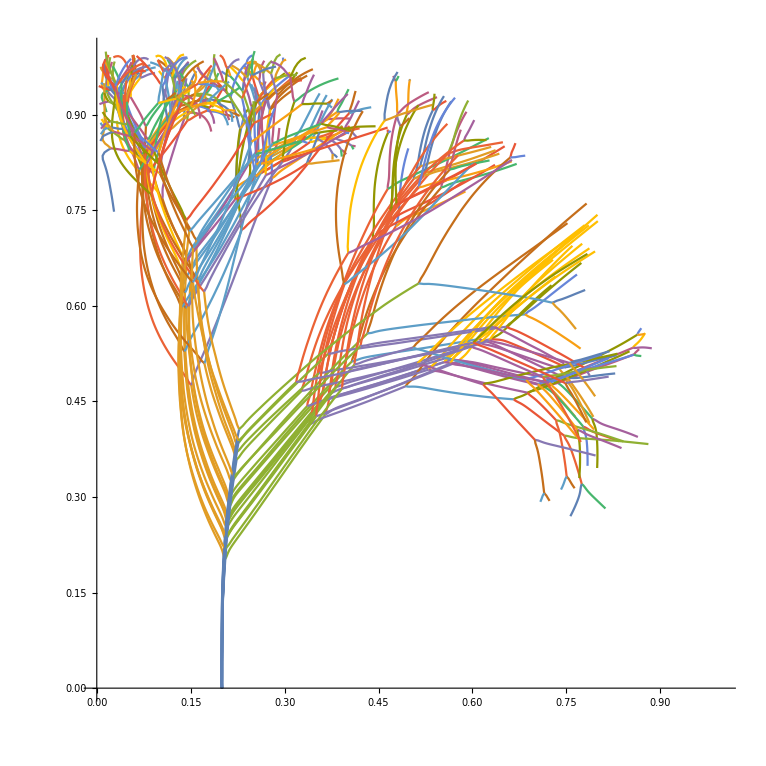

```mathematica
Show[plotJSON[#]&/@SystemDialogInput["FileOpen"]]
```

#### Few smalles(best) ds values. As you can see they are very close to each other

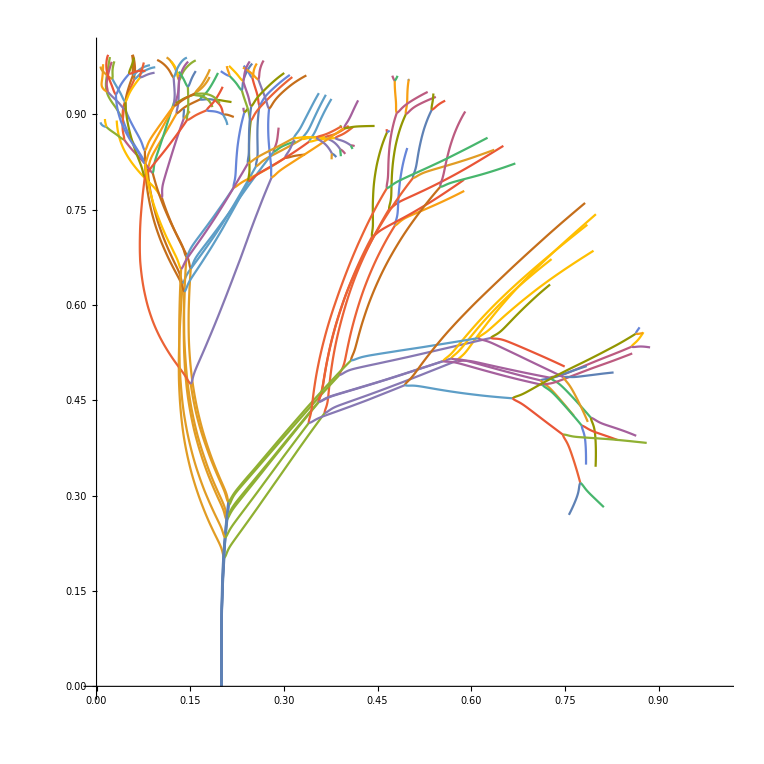

```mathematica
Show[plotJSON[#]&/@SystemDialogInput["FileOpen"]]
```

### Different mesh refinment values from 0.05 to 0.3

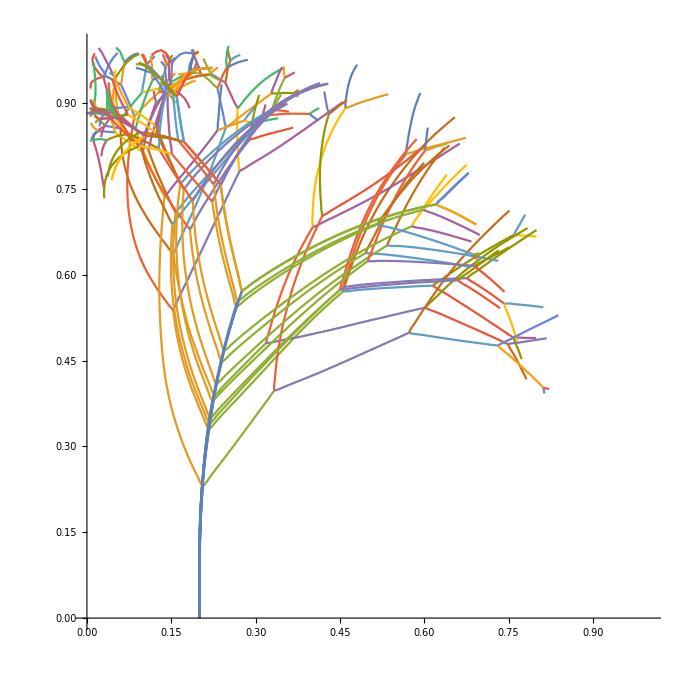

```mathematica
Show[plotJSON[#]&/@SystemDialogInput["FileOpen"]]
```

### Few biggest values of mesh refinment radius. They are pretty close.

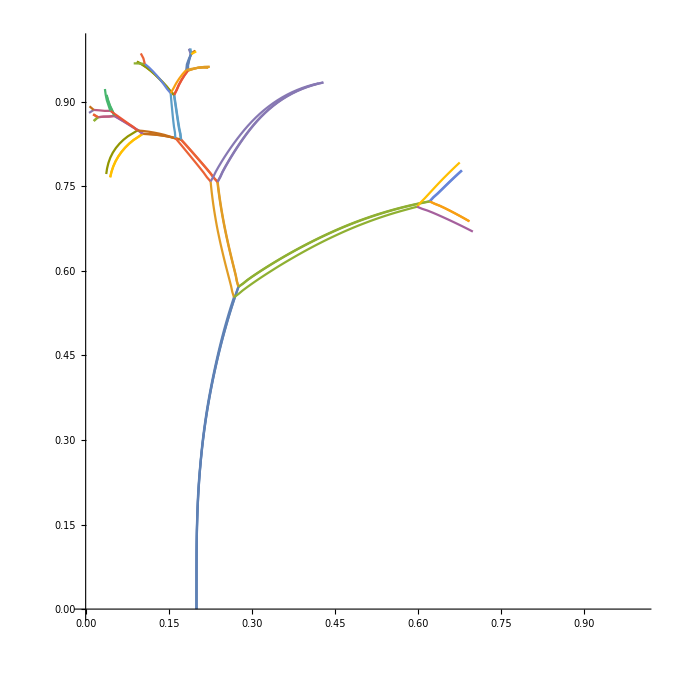

```mathematica
Show[plotJSON[#]&/@SystemDialogInput["FileOpen"]]
```

### Mesh refinment fraction from 0.01 to 0.3

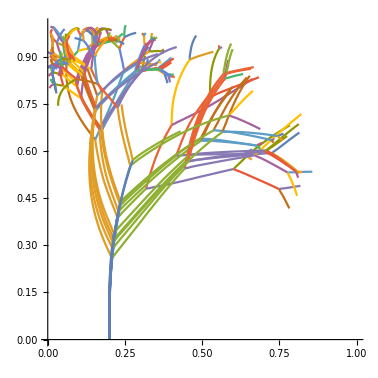

```mathematica
Show[plotJSON[#]&/@SystemDialogInput["FileOpen"]]
```

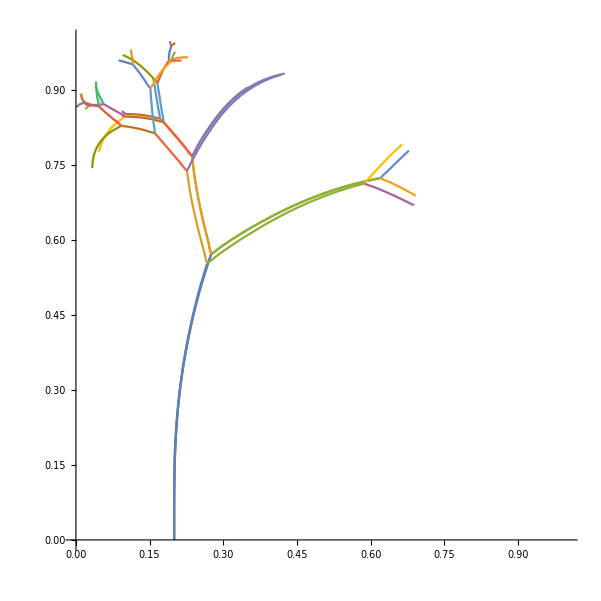

```mathematica
Show[plotJSON[#]&/@SystemDialogInput["FileOpen"]]
```